# Dimensionless 2D Westervelt Cavity: Single Boundary Velocity Excitation

Single boundary velocity shape: sdot(tau) Cos[rExc Pi y/Ly]. Data inputs are current modal state plus instantaneous boundary velocity; targets are modal accelerations.

```mathematica
ClearAll["Global`*"];
nbDir = Quiet[Check[NotebookDirectory[], Directory[]]];
If[! StringQ[nbDir], nbDir = Directory[]];
SetDirectory[nbDir];
Print["Start dimensionless single-excitation 2D Westervelt cavity calculation."];
```

Start dimensionless single-excitation 2D Westervelt cavity calculation.

## Single-Point Response Calculation (Sections 1-4)

### 1. Dimensionless Parameters

```mathematica
(* All quantities are nondimensional. *)
rho0 = 1.;
c0 = 1.;
beta = 1.2;
kappaNL = beta;

Lx = 1.;
Ly = 0.8;
mMax = 2;
nMax = 2;
zetaModal = 0.02;
rExc = 1;
uAmp = 0.1;
omegaFactorSingle = 1;
singlePeriodCount = 80;
stepsPerPeriod = 40.;
observerPoint = {0.63 Lx, 0.41 Ly};

Print["domain = ", {Lx, Ly}, ", mMax = ", mMax, ", nMax = ", nMax, ", rExc = ", rExc];
Print["uAmp = ", uAmp, ", omega factor = ", omegaFactorSingle];
```

domain = {1.,0.8}, mMax = 2, nMax = 2, rExc = 1

uAmp = 0.1, omega factor = 1

### 2. Modes And Single-Excitation Coupling

```mathematica
modeList = DeleteCases[Flatten[Table[{m, n}, {m, 0, mMax}, {n, 0, nMax}], 1], {0, 0}];
Nm = Length[modeList];

normCoef[m_, n_] := Sqrt[(If[m == 0, 1, 2] If[n == 0, 1, 2])/(Lx Ly)];
phiAt[{m_, n_}, x_, y_] := normCoef[m, n] Cos[m Pi x/Lx] Cos[n Pi y/Ly];
omegas = N[Sqrt[(modeList[[All, 1]] Pi/Lx)^2 + (modeList[[All, 2]] Pi/Ly)^2]];
Ddiag = 2 zetaModal omegas;
Kdiag = omegas^2;
identityNm = IdentityMatrix[Nm];
phiObs = N[Table[phiAt[modeList[[i]], observerPoint[[1]], observerPoint[[2]]], {i, Nm}]];

Print["Nm = ", Nm];
Print["modeList = ", modeList];
Print["dimensionless omegas = ", NumberForm[omegas, {8, 4}]];
```

Nm = 8

modeList = {{0,1},{0,2},{1,0},{1,1},{1,2},{2,0},{2,1},{2,2}}

dimensionless omegas = {3.9270,7.8540,3.1416,5.0290,8.4590,6.2832,7.4094,10.0580}

```mathematica
intCos3[a_, b_, c_, len_] := (len/4) (Boole[a + b - c == 0] + Boole[a - b + c == 0] + Boole[-a + b + c == 0] + Boole[a + b + c == 0]);

Ctensor = Table[
   Module[{mi, ni, mj, nj, mk, nk},
    {mi, ni} = modeList[[i]];
    {mj, nj} = modeList[[j]];
    {mk, nk} = modeList[[k]];
    normCoef[mi, ni] normCoef[mj, nj] normCoef[mk, nk]
      intCos3[mi, mj, mk, Lx] intCos3[ni, nj, nk, Ly]
    ],
   {i, Nm}, {j, Nm}, {k, Nm}
   ];
Ctensor = N[Ctensor];
CtForMass = Transpose[Ctensor, {1, 3, 2}];

cosCosInt[a_, b_, len_] := Which[
   a == b == 0, len,
   a == b, len/2,
   True, 0
   ];

gammaVecExc = N[Table[
    normCoef[modeList[[i, 1]], modeList[[i, 2]]] Cos[modeList[[i, 1]] Pi] cosCosInt[modeList[[i, 2]], rExc, Ly],
    {i, Nm}
    ]];

effectiveModeIndexExc = Flatten[Position[Abs[gammaVecExc], _?(# > 10^-10 &)]];
If[effectiveModeIndexExc === {},
  Print["No directly excited acoustic modes for rExc = ", rExc, ". Check mode truncation or excitation shape."];
  Abort[]
  ];
effectiveOmegaExc = omegas[[effectiveModeIndexExc]];
excitationFrequencyCentersAll=Sort[N[effectiveOmegaExc]];
excitationFrequencyCenters=Take[excitationFrequencyCentersAll,1];
omegaExc = omegaFactorSingle First[effectiveOmegaExc];
tauEnd = singlePeriodCount*(2 Pi/omegaExc);

Print["single excitation effective modes = ", modeList[[effectiveModeIndexExc]]];
Print["single excitation effective omegas = ", N[effectiveOmegaExc]];
Print["adaptive excitation frequency centers = ", excitationFrequencyCenters];
Print["omegaExc = ", N[omegaExc], ", omega factor = ", omegaFactorSingle, ", tauEnd = ", N[tauEnd]];
```

single excitation effective modes = {{0,1},{1,1},{2,1}}

single excitation effective omegas = {3.92699,5.029,7.40943}

adaptive excitation frequency centers = {3.92699}

omegaExc = 3.92699, omega factor = 1, tauEnd = 128.

### 3. Single Boundary Velocity Point Calculation

```mathematica
sdotFun[tau_] := -uAmp Sin[omegaExc tau];

rhsFun[tau_?NumericQ, state_?VectorQ] := Module[
   {q, v, sdotNow, mass, dv, kq, nonlinearVelocity, force, acc},
   q = state[[1 ;; Nm]];
   v = state[[Nm + 1 ;; 2 Nm]];
   sdotNow = sdotFun[tau];
   mass = identityNm - 2. kappaNL (CtForMass . q);
   dv = Ddiag v;
   kq = Kdiag q;
   nonlinearVelocity = 2. kappaNL (((v . # . v) &) /@ Ctensor);
   force = -gammaVecExc sdotNow;
   acc = LinearSolve[mass, -dv - kq + nonlinearVelocity + force];
   Join[v, acc]
   ];

maxOmega = Max[Join[{omegaExc}, omegas]];
maxStep = 2 Pi/(stepsPerPeriod maxOmega);
initialState = ConstantArray[0, 2 Nm];
initialState[[1]]=0.1;

Print["Start single-excitation NDSolveValue..."];
sol = Quiet[
   Check[
    NDSolveValue[
     {x'[tau] == rhsFun[tau, x[tau]], x[0] == initialState},
     x,
     {tau, 0, tauEnd},
     Method -> {"StiffnessSwitching"},
     MaxStepFraction -> 1/200,
     MaxStepSize -> maxStep,
     AccuracyGoal -> 8,
     PrecisionGoal -> 8
     ],
    $Failed
    ],
   {NDSolveValue::ndsz, NDSolveValue::ndnum, LinearSolve::luc, General::stop}
   ];

If[sol === $Failed,
  Print["Single-excitation point calculation failed."],
  Print["Single-excitation point calculation finished."]
  ];
```

Start single-excitation NDSolveValue...

Single-excitation point calculation finished.

### 4. Single Point Pressure, Modal Displacements And Field Plots

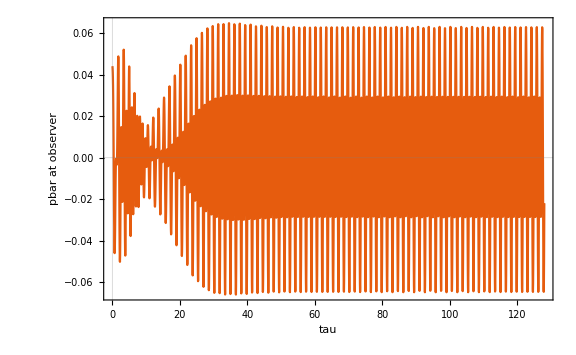
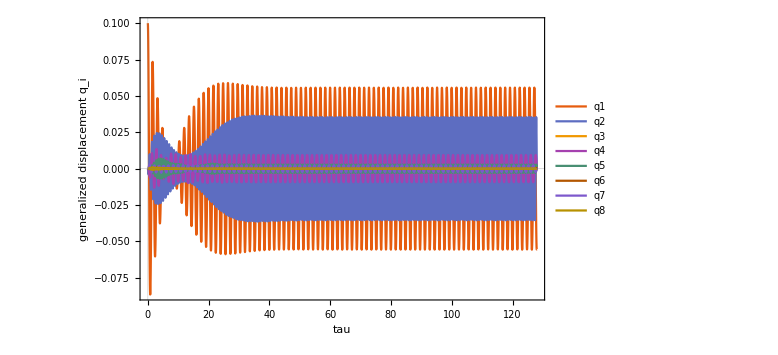
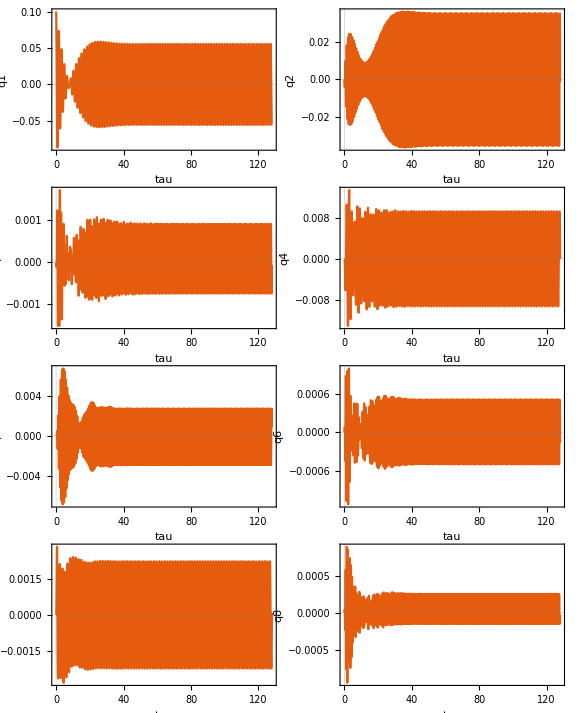
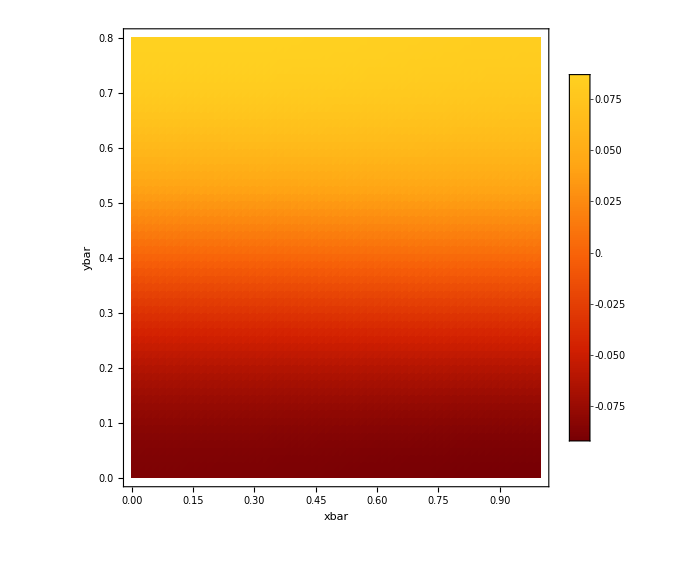

```mathematica
If[!ValueQ[nbDir] || !StringQ[nbDir],
  nbDir = Quiet[Check[NotebookDirectory[], Directory[]]];
  If[!StringQ[nbDir], nbDir = Directory[]]
];

plotDisplay = If[sol === $Failed,
  Print["Skip point plots because the single-excitation solution failed."],

  pObs[tau_?NumericQ] := phiObs . sol[tau][[1 ;; Nm]];

  nPlot = 3000;
  timeGridPlot = N @ Subdivide[0., tauEnd, nPlot - 1];
  timeData = ({#, pObs[#]} &) /@ timeGridPlot;
  qTimeData = Table[Join[{tau}, sol[tau][[1 ;; Nm]]], {tau, timeGridPlot}];
  qLabels = Table["q" <> ToString[i], {i, Nm}];
  qSeriesData = Table[qTimeData[[All, {1, i + 1}]], {i, Nm}];

  pressurePlot = ListLinePlot[
    timeData,
    Frame -> True,
    FrameLabel -> {"tau", "pbar at observer"},
    PlotRange -> All,
    ImageSize -> Large,
    PlotTheme -> "Scientific"
  ];

  qDisplacementPlot = ListLinePlot[
    qSeriesData,
    Frame -> True,
    FrameLabel -> {"tau", "generalized displacement q_i"},
    PlotLegends -> Placed[qLabels, Right],
    PlotRange -> All,
    ImageSize -> Large,
    PlotTheme -> "Scientific"
  ];

  qComponentPlots = Table[
    ListLinePlot[
      qSeriesData[[i]],
      Frame -> True,
      FrameLabel -> {"tau", qLabels[[i]]},
      PlotRange -> All,
      ImageSize -> Medium,
      PlotTheme -> "Scientific"
    ],
    {i, Nm}
  ];
  qDisplacementGridPlot = GraphicsGrid[Partition[qComponentPlots, UpTo[2]], Spacings -> {0.6, 0.8}, ImageSize -> Large];

  Export[
    FileNameJoin[{nbDir, "westervelt_2D_pressure_time_history_dimensionless_single.xlsx"}],
    timeData
  ];
  Export[
    FileNameJoin[{nbDir, "westervelt_2D_pressure_time_history_dimensionless_single.png"}],
    pressurePlot,
    ImageResolution -> 300
  ];
  Export[
    FileNameJoin[{nbDir, "westervelt_2D_generalized_displacement_time_history_dimensionless_single.xlsx"}],
    Prepend[qTimeData, Join[{"tau"}, qLabels]]
  ];
  Export[
    FileNameJoin[{nbDir, "westervelt_2D_generalized_displacement_time_history_dimensionless_single.png"}],
    qDisplacementPlot,
    ImageResolution -> 300
  ];
  Export[
    FileNameJoin[{nbDir, "westervelt_2D_generalized_displacement_components_dimensionless_single.png"}],
    qDisplacementGridPlot,
    ImageResolution -> 300
  ];

  tauField = tauEnd;
  qField = sol[tauField][[1 ;; Nm]];
  pField[x_?NumericQ, y_?NumericQ] := qField . Table[phiAt[modeList[[i]], x, y], {i, Nm}];

  fieldPlot = DensityPlot[
    pField[x, y],
    {x, 0, Lx}, {y, 0, Ly},
    Frame -> True,
    FrameLabel -> {"xbar", "ybar"},
    PlotLegends -> Automatic,
    ColorFunction -> "SolarColors",
    PlotPoints -> 60,
    MaxRecursion -> 2,
    ImageSize -> Large
  ];

  Export[
    FileNameJoin[{nbDir, "westervelt_2D_pressure_field_dimensionless_single.png"}],
    fieldPlot,
    ImageResolution -> 300
  ];

  Column[{pressurePlot, qDisplacementPlot, qDisplacementGridPlot, fieldPlot}]
];

plotDisplay
```

## 5. Nonparametric Dynamics Data Generation

```mathematica
SeedRandom[20260616];dataDir=FileNameJoin[{nbDir,"cavity_dimensionless_single_nonparam_cases"}];If[!DirectoryQ[dataDir],CreateDirectory[dataDir]];inputDim=2 Nm+1;outputDim=Nm;uAmpList=N[Range[0.01,0.11,0.01]];omegaCoarseRangeData={2,8};omegaCoarseStepData=0.2;omegaFactorFineRangesData={{0.98,1.02}};omegaFactorFineStepData=0.002;factorGridData[{fMin_,fMax_},fStep_]:=N[Round[Range[fMin,fMax+fStep/10,fStep],1/10^12]];omegaCoarseListData=factorGridData[omegaCoarseRangeData,omegaCoarseStepData];omegaFactorFineListData=DeleteDuplicates[Sort[Flatten[(factorGridData[#1,omegaFactorFineStepData]&)/@omegaFactorFineRangesData]],Abs[#1-#2]<1/10^10&];omegaFactorList=omegaFactorFineListData;zetaModalData=0.02;excitationFrequencyCenters=DeleteDuplicates[Sort[N[If[ValueQ[excitationFrequencyCentersAll],excitationFrequencyCentersAll,effectiveOmegaExc]]],Abs[#1-#2]<1/10^10&];If[excitationFrequencyCenters==={},Print["No adaptive linear excitation frequency centers found. Check rExc, mMax, nMax, and gammaVecExc."];Abort[]];Print["adaptive linear excitation frequency centers for data generation = ",excitationFrequencyCenters];Print["  coarse omega range = ",omegaCoarseRangeData,", step = ",omegaCoarseStepData,", count = ",Length[omegaCoarseListData]];Print["  fine omega-factor ranges = ",omegaFactorFineRangesData,", step = ",omegaFactorFineStepData];Print["  fine omega-factor count = ",Length[omegaFactorFineListData],", factors = ",omegaFactorFineListData];omegaList=DeleteDuplicates[Sort[Join[omegaCoarseListData,Flatten[Table[fac om0,{om0,excitationFrequencyCenters},{fac,omegaFactorFineListData}]]]],Abs[#1-#2]<1/10^10&];qDecayInitAmp=0.35;uAmpZeroTolData=1/10^12;qZeroTolData=1./10^8;zeroPlateauCountData=20;drivenModeIndexData=First[effectiveModeIndexExc];zeroStateData=ConstantArray[0.,2 Nm];initialDisplacementModeIndexData=1;initialDisplacementData=0.1;qInitialDisplacementData=ReplacePart[ConstantArray[0.,Nm],initialDisplacementModeIndexData->initialDisplacementData];initialDisplacementStateData=Join[qInitialDisplacementData,ConstantArray[0.,Nm]];initialStateListData={zeroStateData};initialStateLabelListData={"zeroState"};decayInitStateData=Join[ReplacePart[ConstantArray[0.,Nm],drivenModeIndexData->qDecayInitAmp],ConstantArray[0.,Nm]];initConfigCountData=Length[initialStateListData];periodCountData=50;samplesPerPeriodData=200;trainRatio=0.7;valRatio=0.15;localStateAugmentationEnabled=True;localStateAugmentationCopies=4;localStateAugmentationApplyToValidation=True;localStateAugmentationApplyToTest=False;localStateAugmentationRelativeScale=0.2;localStateAugmentationDisplacementFloor=5./10^4;localStateAugmentationVelocityFloorVector=localStateAugmentationDisplacementFloor omegas;localStateAugmentationFloorVector=Join[ConstantArray[localStateAugmentationDisplacementFloor,Nm],localStateAugmentationVelocityFloorVector];caseGridData=DeleteDuplicatesBy[Tuples[{uAmpList,omegaList,Range[Length[initialStateListData]]}],Round[N[#1],1/10^10]&];totalCasesData=Length[caseGridData];Print["Single-excitation cavity data generation setup:"];Print["  cases = ",totalCasesData,", init config per case = ",initConfigCountData];Print["  inputDim = ",inputDim,", outputDim = ",outputDim];Print["  uAmp list = ",uAmpList];Print["  omegaList length = ",Length[omegaList]];Print["  backbone initial-state policies = ",initialStateLabelListData,"; q(0)=0 and qdot(0)=0"];Print["  local full-state augmentation enabled = ",localStateAugmentationEnabled,", copies/base sample = ",localStateAugmentationCopies,", relative scale = ",localStateAugmentationRelativeScale];Print["  local augmentation applies to train/validation/test = ",{True,localStateAugmentationApplyToValidation,localStateAugmentationApplyToTest}];Print["  local augmentation floor vector = ",localStateAugmentationFloorVector];Print["  trajectory max periods = ",periodCountData,", samples per period = ",samplesPerPeriodData];Print["  periodic steady-state truncation disabled; full forced-response trajectories are retained"];Print["  output directory = ",dataDir];
```

adaptive linear excitation frequency centers for data generation = {3.92699,5.029,7.40943}

coarse omega range = {2,8}, step = 0.2, count = 31

fine omega-factor ranges = {{0.98,1.02}}, step = 0.002

fine omega-factor count = 21, factors = {0.98,0.982,0.984,0.986,0.988,0.99,0.992,0.994,0.996,0.998,1.,1.002,1.004,1.006,1.008,1.01,1.012,1.014,1.016,1.018,1.02}

Single-excitation cavity data generation setup:

cases = 1034, init config per case = 1

inputDim = 17, outputDim = 8

uAmp list = {0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11}

omegaList length = 94

backbone initial-state policies = {zeroState}; q(0)=0 and qdot(0)=0

local full-state augmentation enabled = True, copies/base sample = 4, relative scale = 0.2

local augmentation applies to train/validation/test = {True,True,False}

local augmentation floor vector = {0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0019635,0.00392699,0.0015708,0.0025145,0.0042295,0.00314159,0.00370472,0.005029}

trajectory max periods = 50, samples per period = 200

periodic steady-state truncation disabled; full forced-response trajectories are retained

output directory = C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases

```mathematica
successCountData=0;failedCountData=0;successfulTrajectoryCountData=0;failedTrajectoryCountData=0;truncatedTrajectoryCountData=0;caseSummaryData={};DdiagData=2 zetaModalData omegas;KdiagData=omegas^2;If[Length[Kernels[]]==0,LaunchKernels[]];parallelKernelCountData=Length[Kernels[]];dataReadDir=dataDir;If[!DirectoryQ[dataReadDir],CreateDirectory[dataReadDir]];oldGeneratedFiles=DeleteDuplicates[Join[FileNames["*_train.mx",dataReadDir],FileNames["*_val.mx",dataReadDir],FileNames["*_test.mx",dataReadDir],FileNames["case_summary_dimensionless.csv",dataReadDir],FileNames["active_mode_phase_metrics_dimensionless.csv",dataReadDir],FileNames["trainData_cavity_dimensionless.mx",dataReadDir],FileNames["valData_cavity_dimensionless.mx",dataReadDir],FileNames["testData_cavity_dimensionless.mx",dataReadDir],FileNames["normParams_cavity_dimensionless.mx",dataReadDir]]];If[oldGeneratedFiles=!={},DeleteFile/@Select[oldGeneratedFiles,FileExistsQ]];Print["Parallel single-excitation case generation:"];Print["  kernels = ",parallelKernelCountData];Print["  output directory = ",dataReadDir];Print["  cleaned old generated files = ",Length[oldGeneratedFiles]];If[Length[localStateAugmentationFloorVector]=!=2 Nm,Print["ERROR: localStateAugmentationFloorVector length must equal 2 Nm."];Abort[]];currentCombinationData=0;successCountProgressData=0;failedCountProgressData=0;counterLockData=Unique["counterLockData$"];SetSharedVariable[currentCombinationData,successCountProgressData,failedCountProgressData];DistributeDefinitions[Nm,omegas,identityNm,kappaNL,CtForMass,Ctensor,gammaVecExc,DdiagData,KdiagData,caseGridData,zeroStateData,initialDisplacementModeIndexData,initialDisplacementData,qInitialDisplacementData,initialDisplacementStateData,initialStateListData,initialStateLabelListData,initConfigCountData,decayInitStateData,uAmpZeroTolData,periodCountData,samplesPerPeriodData,trainRatio,valRatio,qZeroTolData,zeroPlateauCountData,dataReadDir,totalCasesData,counterLockData,localStateAugmentationEnabled,localStateAugmentationCopies,localStateAugmentationApplyToValidation,localStateAugmentationApplyToTest,localStateAugmentationRelativeScale,localStateAugmentationFloorVector];caseResultListData=ParallelTable[Module[{caseU,caseOmega,caseInitIndex,periodData,tauEndData,dtSampleData,tGridData,samples,successfulInitCount,failedInitCount,truncatedInitCount,initialStateCase,initLabelData,sdotData,rhsData,accelerationFromInputData,perturbStateData,localAugmentRuleData,localAugmentDatasetData,solCase,domainEndData,tGridEvalData,stateValsData,derivValsData,zeroFlagsData,zeroWindowStartsData,zeroKeepCountData,keepCountData,tGridUsedData,stateValsUsedData,derivValsUsedData,caseData,caseName,shuffledData,splitIdx1,splitIdx2,trainCaseData,valCaseData,testCaseData,trainBaseCountData,valBaseCountData,testBaseCountData,caseStatusData,exportOkData,caseSummaryRow,caseFailedData,percentTextData,tt,xx,periodicDetectedData,periodicStartPeriodData,periodicStopPeriodData,periodicErrorAtStartData,zeroTruncatedData,truncationReasonData},caseU=caseGridData⟦caseIndex,1⟧;caseOmega=caseGridData⟦caseIndex,2⟧;caseInitIndex=caseGridData⟦caseIndex,3⟧;SeedRandom[Mod[Hash[{caseIndex,caseU,caseOmega,caseInitIndex}],2^31-1]];periodData=(2 π)/caseOmega;tauEndData=periodCountData periodData;dtSampleData=periodData/samplesPerPeriodData;tGridData=N[Range[0.,tauEndData,dtSampleData]];samples={};successfulInitCount=0;failedInitCount=0;truncatedInitCount=0;initialStateCase=initialStateListData⟦caseInitIndex⟧;initLabelData=initialStateLabelListData⟦caseInitIndex⟧;sdotData[tt_]:=-caseU Sin[caseOmega tt];rhsData[tt_?NumericQ,state_?VectorQ]:=Module[{q,v,sdotNow,mass,dv,kq,nonlinearVelocity,force,acc},q=state⟦1;;Nm⟧;v=state⟦Nm+1;;2 Nm⟧;sdotNow=sdotData[tt];mass=identityNm-2. kappaNL CtForMass.q;dv=DdiagData v;kq=KdiagData q;nonlinearVelocity=2. kappaNL (v.#1.v&)/@Ctensor;force=-gammaVecExc sdotNow;acc=LinearSolve[mass,-dv-kq+nonlinearVelocity+force];Join[v,acc]];accelerationFromInputData[input_?VectorQ]:=Module[{state,q,v,sdotNow,mass,dv,kq,nonlinearVelocity,force,acc},If[Length[input]=!=2 Nm+1,Return[Nothing]];state=N[input⟦1;;2 Nm⟧];q=state⟦1;;Nm⟧;v=state⟦Nm+1;;2 Nm⟧;sdotNow=N[input⟦-1⟧];mass=identityNm-2. kappaNL CtForMass.q;dv=DdiagData v;kq=KdiagData q;nonlinearVelocity=2. kappaNL (v.#1.v&)/@Ctensor;force=-gammaVecExc sdotNow;acc=Quiet[Check[LinearSolve[mass,-dv-kq+nonlinearVelocity+force],$Failed],{LinearSolve::luc,General::stop}];If[acc===$Failed||!VectorQ[acc,NumericQ]||Length[acc]=!=Nm||!FreeQ[acc,_Complex|Indeterminate|ComplexInfinity|DirectedInfinity[_]],Nothing,N[Join[state,{sdotNow}]]->N[acc]]];perturbStateData[state_?VectorQ]:=Module[{scale},scale=localStateAugmentationRelativeScale MapThread[Max[Abs[#1],#2]&,{state,localStateAugmentationFloorVector}];N[state+RandomReal[{-1.,1.},2 Nm] scale]];localAugmentRuleData[rule_Rule]:=Module[{input,state,sdotNow},If[!TrueQ[localStateAugmentationEnabled]||localStateAugmentationCopies≤0,Return[{rule}]];input=N[rule⟦1⟧];state=input⟦1;;2 Nm⟧;sdotNow=input⟦-1⟧;Join[{rule},Table[accelerationFromInputData[Join[perturbStateData[state],{sdotNow}]],{localStateAugmentationCopies}]]];localAugmentDatasetData[dataset_,datasetName_String,applyQ_]:=Module[{aug},If[!TrueQ[applyQ],Return[dataset]];SeedRandom[Mod[Hash[{caseName,datasetName,localStateAugmentationCopies,localStateAugmentationRelativeScale}],2^31-1]];aug=DeleteCases[Flatten[localAugmentRuleData/@dataset,1],Nothing];RandomSample[aug]];solCase=Quiet[Check[NDSolveValue[{xx'[tt]==rhsData[tt,xx[tt]],xx[0]==initialStateCase},xx,{tt,0,tauEndData},Method->{"StiffnessSwitching"},MaxStepSize->dtSampleData/2,AccuracyGoal->8,PrecisionGoal->8],$Failed],{NDSolveValue::ndsz,NDSolveValue::ndnum,LinearSolve::luc,General::stop}];If[solCase===$Failed,failedInitCount++,domainEndData=Quiet[Check[solCase["Domain"]⟦1,2⟧,0.]];If[!NumericQ[domainEndData]||domainEndData<0.999 tauEndData,failedInitCount++,tGridEvalData=Select[tGridData,#1≤Min[domainEndData,tauEndData]&];stateValsData=Quiet[Check[N[solCase/@tGridEvalData],$Failed]];If[stateValsData===$Failed||!MatrixQ[stateValsData,NumericQ]||Dimensions[stateValsData]⟦2⟧=!=2 Nm||!FreeQ[stateValsData,_Complex|Indeterminate|ComplexInfinity|DirectedInfinity[_]],failedInitCount++,derivValsData=Quiet[Check[Table[N[rhsData[tGridEvalData⟦ii⟧,stateValsData⟦ii⟧]],{ii,Length[tGridEvalData]}],$Failed],{LinearSolve::luc,General::stop}];If[derivValsData===$Failed||!MatrixQ[derivValsData,NumericQ]||Dimensions[derivValsData]⟦2⟧=!=2 Nm||!FreeQ[derivValsData,_Complex|Indeterminate|ComplexInfinity|DirectedInfinity[_]],failedInitCount++,zeroFlagsData=Table[Norm[stateValsData⟦ii,1;;Nm⟧]<qZeroTolData&&Norm[stateValsData⟦ii,Nm+1;;2 Nm⟧]<qZeroTolData&&Norm[derivValsData⟦ii,Nm+1;;2 Nm⟧]<qZeroTolData,{ii,Length[tGridEvalData]}];zeroWindowStartsData=Flatten[Position[Partition[zeroFlagsData,zeroPlateauCountData,1],{True..}]];zeroKeepCountData=If[zeroWindowStartsData==={},Length[tGridEvalData],Min[Length[tGridEvalData],First[zeroWindowStartsData]+zeroPlateauCountData-1]];periodicDetectedData=False;periodicStartPeriodData=Missing["NotDetected"];periodicStopPeriodData=Missing["NotDetected"];periodicErrorAtStartData=Missing["NotDetected"];keepCountData=zeroKeepCountData;zeroTruncatedData=zeroKeepCountData<Length[tGridEvalData];truncationReasonData=If[zeroTruncatedData,"nearZero","fullLength"];If[keepCountData<Length[tGridEvalData],truncatedInitCount++];tGridUsedData=tGridEvalData⟦1;;keepCountData⟧;stateValsUsedData=stateValsData⟦1;;keepCountData⟧;derivValsUsedData=derivValsData⟦1;;keepCountData⟧;caseData=Table[Join[stateValsUsedData⟦ii⟧,{N[sdotData[tGridUsedData⟦ii⟧]]}]->derivValsUsedData⟦ii,Nm+1;;2 Nm⟧,{ii,Length[tGridUsedData]}];If[caseData==={}||!FreeQ[caseData,_Complex|Indeterminate|ComplexInfinity|DirectedInfinity[_]],failedInitCount++,samples=Join[samples,caseData];successfulInitCount++;];];];];];caseName="case_"<>IntegerString[caseIndex,10,6]<>"_u_"<>StringReplace[ToString[caseU],{" "->"","."->"p","-"->"m"}]<>"_w_"<>StringReplace[ToString[caseOmega],{" "->"","."->"p","-"->"m"}]<>"_"<>initLabelData;If[samples==={},caseSummaryRow={caseName,caseU,caseOmega,initLabelData,successfulInitCount,failedInitCount,truncatedInitCount,0,0,0,0,0,0,0,False,Missing["NotDetected"],Missing["NotDetected"],Missing["NotDetected"],False,"failed","failed"};,shuffledData=RandomSample[samples];splitIdx1=Round[trainRatio Length[shuffledData]];splitIdx2=Round[(trainRatio+valRatio) Length[shuffledData]];trainCaseData=Take[shuffledData,UpTo[splitIdx1]];valCaseData=Take[Drop[shuffledData,splitIdx1],UpTo[Max[splitIdx2-splitIdx1,0]]];testCaseData=Drop[shuffledData,splitIdx2];trainBaseCountData=Length[trainCaseData];valBaseCountData=Length[valCaseData];testBaseCountData=Length[testCaseData];trainCaseData=localAugmentDatasetData[trainCaseData,"train",True];valCaseData=localAugmentDatasetData[valCaseData,"val",localStateAugmentationApplyToValidation];testCaseData=localAugmentDatasetData[testCaseData,"test",localStateAugmentationApplyToTest];exportOkData=Quiet[Check[Export[FileNameJoin[{dataReadDir,caseName<>"_train.mx"}],trainCaseData,"MX"];True,False]]&&Quiet[Check[Export[FileNameJoin[{dataReadDir,caseName<>"_val.mx"}],valCaseData,"MX"];True,False]]&&Quiet[Check[Export[FileNameJoin[{dataReadDir,caseName<>"_test.mx"}],testCaseData,"MX"];True,False]];caseStatusData=If[!exportOkData,"exportFailed",If[failedInitCount>0,"partial","ok"]];caseSummaryRow={caseName,caseU,caseOmega,initLabelData,successfulInitCount,failedInitCount,truncatedInitCount,Length[shuffledData],trainBaseCountData,valBaseCountData,testBaseCountData,Length[trainCaseData],Length[valCaseData],Length[testCaseData],periodicDetectedData,periodicStartPeriodData,periodicStopPeriodData,periodicErrorAtStartData,zeroTruncatedData,truncationReasonData,caseStatusData};];caseFailedData=caseSummaryRow⟦-1⟧==="failed"||caseSummaryRow⟦-1⟧==="exportFailed";CriticalSection[counterLockData,currentCombinationData++;If[caseFailedData,failedCountProgressData++,successCountProgressData++];If[Mod[currentCombinationData,30]==0||currentCombinationData==totalCasesData,percentTextData=ToString[("100.0" currentCombinationData)/Max["1",totalCasesData],OutputForm];Print["progress ",currentCombinationData,"/",totalCasesData," (",percentTextData,"%)","  ok=",successCountProgressData,"  failed=",failedCountProgressData];];];Association["summary"->caseSummaryRow,"successCase"->If[caseFailedData,0,1],"failedCase"->If[caseFailedData,1,0],"successfulTrajectory"->successfulInitCount,"failedTrajectory"->failedInitCount,"truncatedTrajectory"->truncatedInitCount]],{caseIndex,totalCasesData},Method->"CoarsestGrained"];caseSummaryData=caseResultListData⟦All,"summary"⟧;successCountData=Total[caseResultListData⟦All,"successCase"⟧];failedCountData=Total[caseResultListData⟦All,"failedCase"⟧];successfulTrajectoryCountData=Total[caseResultListData⟦All,"successfulTrajectory"⟧];failedTrajectoryCountData=Total[caseResultListData⟦All,"failedTrajectory"⟧];truncatedTrajectoryCountData=Total[caseResultListData⟦All,"truncatedTrajectory"⟧];Export[FileNameJoin[{dataReadDir,"case_summary_dimensionless.csv"}],Prepend[caseSummaryData,{"caseName","uAmp","omega","initType","successfulTrajectory","failedTrajectory","truncatedTrajectory","baseSamples","trainBase","valBase","testBase","trainAugmented","valAugmented","testAugmented","periodicDetected","periodicStartPeriod","periodicStopPeriod","periodicErrorAtStart","zeroTruncated","truncationReason","status"}],"CSV"];Print["Per-case parallel generation finished: okCases=",successCountData,", failedCases=",failedCountData,", okTraj=",successfulTrajectoryCountData,", failedTraj=",failedTrajectoryCountData,", truncatedTraj=",truncatedTrajectoryCountData];Print["Generated case files are saved in ",dataReadDir];
```

Parallel single-excitation case generation:

kernels = 24

output directory = C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases

cleaned old generated files = 360

progress 10/1034 (0.967118%)  ok=10  failed=0

progress 20/1034 (1.93424%)  ok=20  failed=0

progress 30/1034 (2.90135%)  ok=30  failed=0

progress 40/1034 (3.86847%)  ok=40  failed=0

progress 50/1034 (4.83559%)  ok=50  failed=0

progress 60/1034 (5.80271%)  ok=60  failed=0

progress 70/1034 (6.76983%)  ok=70  failed=0

progress 80/1034 (7.73694%)  ok=80  failed=0

progress 90/1034 (8.70406%)  ok=90  failed=0

progress 100/1034 (9.67118%)  ok=100  failed=0

progress 110/1034 (10.6383%)  ok=110  failed=0

progress 120/1034 (11.6054%)  ok=120  failed=0

progress 130/1034 (12.5725%)  ok=130  failed=0

progress 140/1034 (13.5397%)  ok=140  failed=0

progress 150/1034 (14.5068%)  ok=150  failed=0

progress 160/1034 (15.4739%)  ok=160  failed=0

progress 170/1034 (16.441%)  ok=170  failed=0

progress 180/1034 (17.4081%)  ok=180  failed=0

progress 190/1034 (18.3752%)  ok=190  failed=0

progress 200/1034 (19.3424%)  ok=200  failed=0

progress 210/1034 (20.3095%)  ok=210  failed=0

progress 220/1034 (21.2766%)  ok=220  failed=0

progress 230/1034 (22.2437%)  ok=230  failed=0

progress 240/1034 (23.2108%)  ok=240  failed=0

progress 250/1034 (24.1779%)  ok=250  failed=0

progress 260/1034 (25.1451%)  ok=260  failed=0

progress 270/1034 (26.1122%)  ok=270  failed=0

progress 280/1034 (27.0793%)  ok=280  failed=0

progress 290/1034 (28.0464%)  ok=290  failed=0

progress 300/1034 (29.0135%)  ok=300  failed=0

progress 310/1034 (29.9807%)  ok=310  failed=0

progress 320/1034 (30.9478%)  ok=320  failed=0

progress 330/1034 (31.9149%)  ok=330  failed=0

progress 340/1034 (32.882%)  ok=340  failed=0

progress 350/1034 (33.8491%)  ok=350  failed=0

progress 360/1034 (34.8162%)  ok=360  failed=0

progress 370/1034 (35.7834%)  ok=370  failed=0

progress 380/1034 (36.7505%)  ok=380  failed=0

progress 390/1034 (37.7176%)  ok=390  failed=0

progress 400/1034 (38.6847%)  ok=400  failed=0

progress 410/1034 (39.6518%)  ok=410  failed=0

progress 420/1034 (40.619%)  ok=420  failed=0

progress 430/1034 (41.5861%)  ok=430  failed=0

progress 440/1034 (42.5532%)  ok=440  failed=0

progress 450/1034 (43.5203%)  ok=450  failed=0

progress 460/1034 (44.4874%)  ok=460  failed=0

progress 470/1034 (45.4545%)  ok=470  failed=0

progress 480/1034 (46.4217%)  ok=480  failed=0

progress 490/1034 (47.3888%)  ok=490  failed=0

progress 500/1034 (48.3559%)  ok=500  failed=0

progress 510/1034 (49.323%)  ok=510  failed=0

progress 520/1034 (50.2901%)  ok=520  failed=0

progress 530/1034 (51.2573%)  ok=530  failed=0

progress 540/1034 (52.2244%)  ok=540  failed=0

progress 550/1034 (53.1915%)  ok=550  failed=0

progress 560/1034 (54.1586%)  ok=560  failed=0

progress 570/1034 (55.1257%)  ok=570  failed=0

progress 580/1034 (56.0928%)  ok=580  failed=0

progress 590/1034 (57.06%)  ok=590  failed=0

progress 600/1034 (58.0271%)  ok=600  failed=0

progress 610/1034 (58.9942%)  ok=610  failed=0

progress 620/1034 (59.9613%)  ok=620  failed=0

progress 630/1034 (60.9284%)  ok=630  failed=0

progress 640/1034 (61.8956%)  ok=640  failed=0

progress 650/1034 (62.8627%)  ok=650  failed=0

progress 660/1034 (63.8298%)  ok=660  failed=0

progress 670/1034 (64.7969%)  ok=670  failed=0

progress 680/1034 (65.764%)  ok=680  failed=0

progress 690/1034 (66.7311%)  ok=690  failed=0

progress 700/1034 (67.6983%)  ok=700  failed=0

progress 710/1034 (68.6654%)  ok=710  failed=0

progress 720/1034 (69.6325%)  ok=720  failed=0

progress 730/1034 (70.5996%)  ok=730  failed=0

progress 740/1034 (71.5667%)  ok=740  failed=0

progress 750/1034 (72.5338%)  ok=750  failed=0

progress 760/1034 (73.501%)  ok=760  failed=0

progress 770/1034 (74.4681%)  ok=770  failed=0

progress 780/1034 (75.4352%)  ok=780  failed=0

progress 790/1034 (76.4023%)  ok=790  failed=0

progress 800/1034 (77.3694%)  ok=800  failed=0

progress 810/1034 (78.3366%)  ok=810  failed=0

progress 820/1034 (79.3037%)  ok=820  failed=0

progress 830/1034 (80.2708%)  ok=830  failed=0

progress 840/1034 (81.2379%)  ok=840  failed=0

progress 850/1034 (82.205%)  ok=850  failed=0

progress 860/1034 (83.1721%)  ok=860  failed=0

progress 870/1034 (84.1393%)  ok=870  failed=0

progress 880/1034 (85.1064%)  ok=880  failed=0

progress 890/1034 (86.0735%)  ok=890  failed=0

progress 900/1034 (87.0406%)  ok=900  failed=0

progress 910/1034 (88.0077%)  ok=910  failed=0

progress 920/1034 (88.9749%)  ok=920  failed=0

progress 930/1034 (89.942%)  ok=930  failed=0

progress 940/1034 (90.9091%)  ok=940  failed=0

progress 950/1034 (91.8762%)  ok=950  failed=0

progress 960/1034 (92.8433%)  ok=960  failed=0

progress 970/1034 (93.8104%)  ok=970  failed=0

progress 980/1034 (94.7776%)  ok=980  failed=0

progress 990/1034 (95.7447%)  ok=990  failed=0

progress 1000/1034 (96.7118%)  ok=1000  failed=0

progress 1010/1034 (97.6789%)  ok=1010  failed=0

progress 1020/1034 (98.646%)  ok=1020  failed=0

progress 1030/1034 (99.6132%)  ok=1030  failed=0

progress 1034/1034 (100.%)  ok=1034  failed=0

Per-case parallel generation finished: okCases=1034, failedCases=0, okTraj=1034, failedTraj=0, truncatedTraj=0

Generated case files are saved in C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases

```mathematica
readDirData = If[ValueQ[dataReadDir] && StringQ[dataReadDir] && DirectoryQ[dataReadDir], dataReadDir, dataDir];

Print["Reading generated case files from ", readDirData];

kTrainPerCase = 1000;
kValPerCase =200;
kTestPerCase = 200;

useActiveModeTraining = True;
activeModeSelectionMethod = "automatic phase-space response metric";
phaseMetricSamplesPerFile = 1200;
phaseMetricMaxFiles = 120;
phaseMetricRelativeThreshold = 10^-3;
phaseMetricAbsoluteThreshold = 10^-6;
activeModeDetectionUseTrainOnly = True;

trainFiles = FileNames["*_train.mx", readDirData];
valFiles = FileNames["*_val.mx", readDirData];
testFiles = FileNames["*_test.mx", readDirData];

Print["Found case files: train=", Length[trainFiles], "  val=", Length[valFiles], "  test=", Length[testFiles]];
If[trainFiles === {} || valFiles === {} || testFiles === {},
  Print["No train/val/test files found in ", readDirData];
  Abort[];
];

ClearAll[CollectPhasePointPairs, EstimateActiveModesFromPhasePointFiles];
CollectPhasePointPairs[files_, maxFiles_, samplesPerFile_] := Module[{sampleFiles, importedData, sampledData, lhs, gathered},
  sampleFiles = Take[RandomSample[files], UpTo[maxFiles]];
  gathered = Reap[
    Do[
      importedData = Quiet[Check[Import[file, "MX"], {}]];
      If[importedData =!= $Failed && importedData =!= {},
        SeedRandom[Mod[Hash[{"phaseMetric", file}], 2^31 - 1]];
        sampledData = RandomSample[importedData, Min[samplesPerFile, Length[importedData]]];
        Scan[
          (lhs = N @ #[[1]];
           If[VectorQ[lhs, NumericQ] && Length[lhs] == 2 Nm + 1,
             Sow[{lhs[[1 ;; Nm]], lhs[[Nm + 1 ;; 2 Nm]]}]
           ]) &,
          sampledData
        ];
      ],
      {file, sampleFiles}
    ]
  ][[2]];
  If[gathered === {}, {}, gathered[[1]]]
];

EstimateActiveModesFromPhasePointFiles[files_] := Module[{phasePointPairs, qMat, vMat, vScaledMat, qStdVec, vScaledStdVec, phaseMetricVec, maxPhaseMetric, phaseMetricRelVec, active, metricRows},
  phasePointPairs = CollectPhasePointPairs[files, phaseMetricMaxFiles, phaseMetricSamplesPerFile];
  If[phasePointPairs === {},
    Return[<|
      "phasePointCount" -> 0,
      "qStd" -> ConstantArray[0., Nm],
      "qdotOverOmegaStd" -> ConstantArray[0., Nm],
      "phaseMetric" -> ConstantArray[0., Nm],
      "relativePhaseMetric" -> ConstantArray[0., Nm],
      "activeModeIndices" -> Range[Nm],
      "metricRows" -> {},
      "fallback" -> "empty phase-point sample; use all modes"
    |>]
  ];
  qMat = phasePointPairs[[All, 1]];
  vMat = phasePointPairs[[All, 2]];
  vScaledMat = (#/omegas) & /@ vMat;
  qStdVec = StandardDeviation /@ Transpose[qMat];
  vScaledStdVec = StandardDeviation /@ Transpose[vScaledMat];
  phaseMetricVec = Sqrt[qStdVec^2 + vScaledStdVec^2];
  maxPhaseMetric = Max[phaseMetricVec];
  phaseMetricRelVec = If[maxPhaseMetric > 0, phaseMetricVec/maxPhaseMetric, ConstantArray[0., Nm]];
  active = Flatten @ Position[
    MapThread[#1 >= phaseMetricAbsoluteThreshold && #2 >= phaseMetricRelativeThreshold &, {phaseMetricVec, phaseMetricRelVec}],
    True
  ];
  If[active === {} && maxPhaseMetric > 0, active = Flatten @ Position[phaseMetricVec, maxPhaseMetric]];
  If[active === {}, active = Range[Nm]];
  active = DeleteDuplicates[active];
  metricRows = Table[
    {i, ToString[modeList[[i]], InputForm], qStdVec[[i]], vScaledStdVec[[i]], phaseMetricVec[[i]], phaseMetricRelVec[[i]], If[MemberQ[active, i], 1, 0]},
    {i, Nm}
  ];
  <|
    "phasePointCount" -> Length[phasePointPairs],
    "qStd" -> qStdVec,
    "qdotOverOmegaStd" -> vScaledStdVec,
    "phaseMetric" -> phaseMetricVec,
    "relativePhaseMetric" -> phaseMetricRelVec,
    "activeModeIndices" -> active,
    "metricRows" -> metricRows,
    "fallback" -> None
  |>
];

phaseMetricSourceFiles = If[activeModeDetectionUseTrainOnly, trainFiles, Join[trainFiles, valFiles, testFiles]];
phaseMetricResult = EstimateActiveModesFromPhasePointFiles[phaseMetricSourceFiles];
activeModeIndices = If[useActiveModeTraining, phaseMetricResult["activeModeIndices"], Range[Nm]];
activeModeIndices = DeleteDuplicates[activeModeIndices];
If[!VectorQ[activeModeIndices, IntegerQ] || !SubsetQ[Range[Nm], activeModeIndices],
  Print["ERROR: activeModeIndices inferred from phase points are invalid: ", activeModeIndices];
  Abort[];
];
inactiveModeIndices = Complement[Range[Nm], activeModeIndices];
activeModeCount = Length[activeModeIndices];
inputDim = 2 activeModeCount + 1;
outputDim = activeModeCount;

phaseMetricFile = FileNameJoin[{readDirData, "active_mode_phase_metrics_dimensionless.csv"}];
Export[
  phaseMetricFile,
  Prepend[phaseMetricResult["metricRows"], {"modeIndex", "modeLabel", "qStd", "qdotOverOmegaStd", "phaseMetric", "relativePhaseMetric", "active"}],
  "CSV"
];

Print["Active-mode training control:"];
Print["  method = ", activeModeSelectionMethod];
Print["  phase metric = Sqrt[Std[q_i]^2 + Std[(q_i dot)/omega_i]^2]"];
Print["  phase-point sample count = ", phaseMetricResult["phasePointCount"], ", source files = ", Min[phaseMetricMaxFiles, Length[phaseMetricSourceFiles]]];
Print["  relative threshold = ", phaseMetricRelativeThreshold, ", absolute threshold = ", phaseMetricAbsoluteThreshold];
Print["  active q modes = ", activeModeIndices, "; inactive q modes = ", inactiveModeIndices];
Print["  phase metric CSV = ", phaseMetricFile];
Print["  training inputDim = ", inputDim, ", outputDim = ", outputDim];

ClearAll[ProjectRuleToActiveModes, SampleProjectedData];
ProjectRuleToActiveModes::dim = "Expected lhs length 2 Nm + 1 and rhs length Nm, got `1`.";
ProjectRuleToActiveModes[rule_Rule] := Module[{lhs, rhs, q, v, sdotNow},
  lhs = N @ rule[[1]];
  rhs = N @ rule[[2]];
  If[Length[lhs] != 2 Nm + 1 || Length[rhs] != Nm,
    Message[ProjectRuleToActiveModes::dim, {Length[lhs], Length[rhs]}];
    Return[$Failed];
  ];
  q = lhs[[1 ;; Nm]];
  v = lhs[[Nm + 1 ;; 2 Nm]];
  sdotNow = lhs[[-1]];
  Join[q[[activeModeIndices]], v[[activeModeIndices]], {sdotNow}] -> rhs[[activeModeIndices]]
];

SampleProjectedData[file_, k_] := Module[{importedData, sampledData, projectedData},
  importedData = Quiet[Check[Import[file, "MX"], {}]];
  If[importedData === $Failed || importedData === {}, Return[{}]];
  SeedRandom[Mod[Hash[file], 2^31 - 1]];
  sampledData = RandomSample[importedData, Min[k, Length[importedData]]];
  projectedData = ProjectRuleToActiveModes /@ sampledData;
  DeleteCases[projectedData, $Failed]
];

trainFiles = RandomSample[trainFiles];
valFiles = RandomSample[valFiles];
testFiles = RandomSample[testFiles];

If[Length[Kernels[]] == 0, LaunchKernels[]];
DistributeDefinitions[Nm, activeModeIndices, ProjectRuleToActiveModes, SampleProjectedData, kTrainPerCase, kValPerCase, kTestPerCase];

trainChunks = ParallelTable[
  SampleProjectedData[trainFile, kTrainPerCase],
  {trainFile, trainFiles},
  Method -> "CoarsestGrained"
];
trainData = Flatten[trainChunks, 1];
Clear[trainChunks];

If[trainData === {},
  Print["Empty train data after fixed-per-case sampling and active-mode projection."];
  Abort[];
];

inputMean = ConstantArray[0., inputDim];
inputM2 = ConstantArray[0., inputDim];
inputN = 0;
targetMean = ConstantArray[0., outputDim];
targetM2 = ConstantArray[0., outputDim];
targetN = 0;

Do[
  inputN++;
  inputDelta = trainData[[ii, 1]] - inputMean;
  inputMean = inputMean + inputDelta/inputN;
  inputDelta2 = trainData[[ii, 1]] - inputMean;
  inputM2 = inputM2 + inputDelta inputDelta2;

  targetN++;
  targetDelta = trainData[[ii, 2]] - targetMean;
  targetMean = targetMean + targetDelta/targetN;
  targetDelta2 = trainData[[ii, 2]] - targetMean;
  targetM2 = targetM2 + targetDelta targetDelta2;
  ,
  {ii, Length[trainData]}
];

inputStd = Sqrt[If[inputN >= 2, inputM2/(inputN - 1), ConstantArray[0., inputDim]]] /. 0. -> 1.;
targetStd = Sqrt[If[targetN >= 2, targetM2/(targetN - 1), ConstantArray[0., outputDim]]] /. 0. -> 1.;

valChunks = ParallelTable[
  SampleProjectedData[valFile, kValPerCase],
  {valFile, valFiles},
  Method -> "CoarsestGrained"
];
valData = Flatten[valChunks, 1];
Clear[valChunks];

testChunks = ParallelTable[
  SampleProjectedData[testFile, kTestPerCase],
  {testFile, testFiles},
  Method -> "CoarsestGrained"
];
testData = Flatten[testChunks, 1];
Clear[testChunks, importedData, inputDelta, inputDelta2, targetDelta, targetDelta2];

If[valData === {} || testData === {},
  Print["Empty val/test data after fixed-per-case sampling and active-mode projection."];
  Abort[];
];

Export[FileNameJoin[{readDirData, "trainData_cavity_dimensionless.mx"}], trainData, "MX"];
Export[FileNameJoin[{readDirData, "valData_cavity_dimensionless.mx"}], valData, "MX"];
Export[FileNameJoin[{readDirData, "testData_cavity_dimensionless.mx"}], testData, "MX"];

normParams = <|
  "inputMean" -> inputMean,
  "inputStd" -> inputStd,
  "targetMean" -> targetMean,
  "targetStd" -> targetStd,
  "inputDim" -> inputDim,
  "outputDim" -> outputDim,
  "fullModeCount" -> Nm,
  "modeList" -> modeList,
  "activeModeTraining" -> useActiveModeTraining,
  "activeModeSelectionMethod" -> activeModeSelectionMethod,
  "activeModeIndices" -> activeModeIndices,
  "inactiveModeIndices" -> inactiveModeIndices,
  "activeModeList" -> modeList[[activeModeIndices]],
  "phaseMetricFile" -> phaseMetricFile,
  "phaseMetricSamplesPerFile" -> phaseMetricSamplesPerFile,
  "phaseMetricMaxFiles" -> phaseMetricMaxFiles,
  "phaseMetricRelativeThreshold" -> phaseMetricRelativeThreshold,
  "phaseMetricAbsoluteThreshold" -> phaseMetricAbsoluteThreshold,
  "phaseMetricPointCount" -> phaseMetricResult["phasePointCount"],
  "phaseMetric" -> phaseMetricResult["phaseMetric"],
  "relativePhaseMetric" -> phaseMetricResult["relativePhaseMetric"],
  "phaseQStd" -> phaseMetricResult["qStd"],
  "phaseQdotOverOmegaStd" -> phaseMetricResult["qdotOverOmegaStd"],
  "omegas" -> omegas,
  "excitationModeIndices" -> effectiveModeIndexExc,
  "excitationModeList" -> modeList[[effectiveModeIndexExc]],
  "excitationFrequencyCenters" -> excitationFrequencyCenters,
  "rExc" -> rExc,
  "zetaModalData" -> zetaModalData,
  "initialDisplacementModeIndexData" -> initialDisplacementModeIndexData,
  "initialDisplacementData" -> initialDisplacementData,
  "qInitialDisplacementData" -> qInitialDisplacementData,
  "initialDisplacementStateData" -> initialDisplacementStateData,
  "initialStateLabelListData" -> initialStateLabelListData,
  "initConfigCountData" -> initConfigCountData,
  "uAmpList" -> uAmpList,
  "omegaList" -> omegaList,
  "omegaFactorList" -> omegaFactorList,
  "omegaCoarseRangeData" -> omegaCoarseRangeData,
  "omegaCoarseStepData" -> omegaCoarseStepData,
  "omegaCoarseListData" -> omegaCoarseListData,
  "omegaFactorFineListData" -> omegaFactorFineListData,
  "omegaFactorFineRangesData" -> omegaFactorFineRangesData,
  "omegaFactorFineStepData" -> omegaFactorFineStepData,
  "caseCount" -> totalCasesData,
  "kTrainPerCase" -> kTrainPerCase,
  "kValPerCase" -> kValPerCase,
  "kTestPerCase" -> kTestPerCase,
  "trainRatio" -> trainRatio,
  "valRatio" -> valRatio,
  "periodCountData" -> periodCountData,
  "samplesPerPeriodData" -> samplesPerPeriodData,
  "inputDefinition" -> "Join[q[[activeModeIndices]], qdot[[activeModeIndices]], {sdot(tau)}]",
  "outputDefinition" -> "qddot[[activeModeIndices]]",
  "deploymentAcceleration" -> "Network output is reinserted into a full Nm acceleration vector; inactive accelerations are forced to zero."
|>;

Print["Welford normalization samples: inputN=", inputN, "  targetN=", targetN];
Print["Merged active-mode dataset sizes: train=", Length[trainData], "  val=", Length[valData], "  test=", Length[testData]];
Print["Example input/output dimensions: ", {Length[trainData[[1, 1]]], Length[trainData[[1, 2]]] }];

Export[FileNameJoin[{readDirData, "normParams_cavity_dimensionless.mx"}], normParams, "MX"];
Print["Saved automatically selected active-mode rule datasets and normParams to ", readDirData];
```

Reading generated case files from C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases

Found case files: train=1034  val=1034  test=1034

Active-mode training control:

method = automatic phase-space response metric

phase metric = Sqrt[Std[q_i]^2 + Std[(q_i dot)/omega_i]^2]

phase-point sample count = 144000, source files = 120

relative threshold = 1/1000, absolute threshold = 1/1000000

active q modes = {1,2,3,4,5,6,7,8}; inactive q modes = {}

phase metric CSV = C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\active_mode_phase_metrics_dimensionless.csv

training inputDim = 17, outputDim = 8

Welford normalization samples: inputN=1034000  targetN=1034000

Merged active-mode dataset sizes: train=1034000  val=206800  test=206800

Example input/output dimensions: {17,8}

Saved automatically selected active-mode rule datasets and normParams to C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases

## 6. Neural Network Training

```mathematica
SetDirectory@NotebookDirectory[];
ClearAll[MyNormalize, EvaluateOnDataset];

Print["Neural network training: dimensionless cavity"];
Print["Input  : Join[{q1,...,qNm,q1dot,...,qNmdot}, {sdot(tau)}]"];
Print["Output : {q1ddot,...,qNmddot}"];

nbDir = NotebookDirectory[];
dataDir = FileNameJoin[{nbDir, "cavity_dimensionless_single_nonparam_cases"}];

trainFile = FileNameJoin[{dataDir, "trainData_cavity_dimensionless.mx"}];
valFile = FileNameJoin[{dataDir, "valData_cavity_dimensionless.mx"}];
testFile = FileNameJoin[{dataDir, "testData_cavity_dimensionless.mx"}];
normFile = FileNameJoin[{dataDir, "normParams_cavity_dimensionless.mx"}];
requiredFiles = {trainFile, valFile, testFile, normFile};
missingFiles = Select[requiredFiles, Not[FileExistsQ[#]] &];
If[Length[missingFiles] > 0,
  Print["ERROR: missing training files:"];
  Print /@ missingFiles;
  Abort[];
  ];

normParams = Import[normFile, "MX"];
inDim = If[KeyExistsQ[normParams, "inputDim"], normParams["inputDim"], Length[normParams["inputMean"]]];

outDim = If[KeyExistsQ[normParams, "outputDim"], normParams["outputDim"], Length[normParams["targetMean"]]];

expectedOutDim = (inDim - 1)/2;

If[IntegerQ[expectedOutDim] && outDim != expectedOutDim,
  Print["ERROR: loaded data uses the old target. Expected output = qddot only."];
  Print["  expected output dimension = ", expectedOutDim, ", loaded output dimension = ", outDim];
  Print["  Please rerun the data generation section before training."];
  Abort[];
  ];

trainData = Import[trainFile, "MX"];
valData = Import[valFile, "MX"];
testData = Import[testFile, "MX"];

Print["Data loaded from: ", dataDir];
Print["  train: ", Length[trainData], " samples"];
Print["  val  : ", Length[valData], " samples"];
Print["  test : ", Length[testData], " samples"];
Print["  total: ", Length[trainData] + Length[valData] + Length[testData], " samples"];

inputMean = N@normParams["inputMean"];
inputStd = N@normParams["inputStd"];
targetMean = N@normParams["targetMean"];
targetStdRaw = N@normParams["targetStd"];
inputStd = Map[If[Abs[#] < 10^-12, 10^-12, #] &, inputStd];
targetStdFloor = Max[10^-8, 10^-6 Max[Abs[targetStdRaw]]];

targetStd = Map[If[Abs[#] < targetStdFloor, targetStdFloor, #] &, targetStdRaw];

targetStdFlooredCount = Count[Map[Abs[#] < targetStdFloor &, targetStdRaw], True];

Print["targetStd floor for training normalization: ", ScientificForm[targetStdFloor, 4]];
Print["targetStd entries floored: ", targetStdFlooredCount, "/", Length[targetStdRaw]];

inDim = If[KeyExistsQ[normParams, "inputDim"], normParams["inputDim"], Length[trainData[[1, 1]]]];
outDim = If[KeyExistsQ[normParams, "outputDim"], normParams["outputDim"], Length[trainData[[1, 2]]]];

If[Length[trainData[[1, 1]]] != inDim || Length[trainData[[1, 2]]] != outDim,
  Print["ERROR: dimension mismatch between normParams and trainData."];
  Print["  normParams input/output = ", {inDim, outDim}];
  Print["  trainData input/output  = ", {Length[trainData[[1, 1]]], Length[trainData[[1, 2]]] }];
  Abort[];
  ];

expectedOutDim = (inDim - 1)/2;

If[IntegerQ[expectedOutDim] && outDim != expectedOutDim,
  Print["ERROR: this training section expects output = qddot only."];
  Print["  expected output dimension = ", expectedOutDim, ", loaded output dimension = ", outDim];
  Print["  Regenerate data with the updated data generation section before training."];
  Abort[];
  ];

Print["input dimension: ", inDim, ", output dimension: ", outDim];
If[KeyExistsQ[normParams, "inputDefinition"], Print["input definition: ", normParams["inputDefinition"]]];
If[KeyExistsQ[normParams, "outputDefinition"], Print["output definition: ", normParams["outputDefinition"]]];

MyNormalize[x_, m_, s_] := (x - m)/s;

Print["Building normalized rule datasets..."];
trainDataNorm = Table[
   MyNormalize[trainData[[i, 1]], inputMean, inputStd] -> MyNormalize[trainData[[i, 2]], targetMean, targetStd],
   {i, Length[trainData]}
   ];
valDataNorm = Table[
   MyNormalize[valData[[i, 1]], inputMean, inputStd] -> MyNormalize[valData[[i, 2]], targetMean, targetStd],
   {i, Length[valData]}
   ];
testDataNorm = Table[
   MyNormalize[testData[[i, 1]], inputMean, inputStd] -> MyNormalize[testData[[i, 2]], targetMean, targetStd],
   {i, Length[testData]}
   ];
Print["Normalized rule datasets are ready."];

(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
net = NetChain[
   {LinearLayer[256], Tanh, LinearLayer[128], Tanh, LinearLayer[outDim]},
   "Input" -> inDim,
   "Output" -> outDim
   ]; 

EvaluateOnDataset[nn_, dataset_, datasetName_String] := Module[
   {inputsNorm, predNormList, pred, true, rmseVec, stdTrueVec, trueGlobalRMS, globalScale, activeTol, activeMask, activeModes, inactiveModes, relErrVec, activeRelErrVec, globalRelErr, score},
   inputsNorm = (MyNormalize[#, inputMean, inputStd] &) /@ dataset[[All, 1]];
   predNormList = nn /@ inputsNorm;
   pred = ((# targetStd + targetMean) &) /@ predNormList;
   true = dataset[[All, 2]];
   rmseVec = Sqrt@Mean[(pred - true)^2];
   stdTrueVec = StandardDeviation /@ Transpose[true];
   trueGlobalRMS = Sqrt[Mean[Flatten[true^2]]];
   globalScale = Max[stdTrueVec];
   activeTol = Max[10^-8, 10^-6 globalScale];
   activeMask = Map[# >= activeTol &, stdTrueVec];
   activeModes = Flatten[Position[activeMask, True]];
   inactiveModes = Flatten[Position[activeMask, False]];
   relErrVec = MapThread[If[#3, 100 #1/(#2 + 10^-12), Missing["Inactive"]] &, {rmseVec, stdTrueVec, activeMask}];
   activeRelErrVec = If[activeModes === {}, {}, relErrVec[[activeModes]]];
   globalRelErr = If[trueGlobalRMS >= activeTol, 100 Sqrt[Mean[Flatten[(pred - true)^2]]]/trueGlobalRMS, Missing["ZeroReference"]];
   score = Mean[rmseVec];
   Print["\n", datasetName, " evaluation:"];
   Print["  RMSE = ", NumberForm[rmseVec, {6, 4}]];
   Print["  Active modes = ", activeModes, "; inactive modes = ", inactiveModes];
   Print["  Rel%(active) = ", If[activeModes === {}, {}, MapThread[Rule, {activeModes, NumberForm[#, {5, 2}] & /@ activeRelErrVec}]]];
   Print["  Global Rel% = ", If[MissingQ[globalRelErr], globalRelErr, NumberForm[globalRelErr, {6, 3}]]];
   Print["  Score = ", NumberForm[score, {6, 4}]];
   <|"rmse" -> rmseVec, "stdTrue" -> stdTrueVec, "rel%" -> relErrVec, "activeModes" -> activeModes, "inactiveModes" -> inactiveModes, "globalRel%" -> globalRelErr, "score" -> score, "datasetName" -> datasetName|>
   ];

stages = {
   <|"rounds" -> 500, "lr" -> 0.005|>,
   <|"rounds" -> 1000, "lr" -> 0.001|>,
   <|"rounds" -> 5000, "lr" -> 0.0005|>,
   <|"rounds" -> 5000, "lr" -> 0.0001|>,
   <|"rounds" -> 1000, "lr" -> 0.00005|>,
   <|"rounds" -> 1000, "lr" -> 0.00001|>
   };

Print["\nStart multi-stage training..."];
bestNet = net;
bestStats = <|"score" -> Infinity|>;
currNet = net;

Do[
  Print["\n========== Stage ", si, " : rounds = ", stages[[si, "rounds"]], ", lr = ", stages[[si, "lr"]], " =========="];
  tr = NetTrain[
    currNet, trainDataNorm, All,
    ValidationSet -> valDataNorm,
    MaxTrainingRounds -> stages[[si, "rounds"]],
    BatchSize -> 4096,
    LearningRate -> stages[[si, "lr"]],
    Method -> {"ADAM"},
    TargetDevice -> "CPU",
    TrainingProgressReporting -> "Panel"
    ];
  currNet = tr["TrainedNet"];
  stats = EvaluateOnDataset[currNet, valData, "validation set"];
  If[stats["score"] < bestStats["score"],
    bestNet = currNet;
    bestStats = stats;
    checkpointFile = FileNameJoin[{dataDir, "checkpoint_cavity_dimensionless_best_stage" <> ToString[si] <> ".wlnet"}];
    Export[checkpointFile, bestNet, "WLNet"];
    Print["Best model updated and saved: ", checkpointFile];
    ];
  ,
  {si, Length[stages]}
  ];

trainedNet = bestNet;

normParamsFinal = Join[
   normParams,
   <|
    "targetStd" -> targetStd,
    "targetStdRaw" -> targetStdRaw,
    "targetStdFloor" -> targetStdFloor,
    "targetStdFlooredCount" -> targetStdFlooredCount,
    "targetNormalization" -> "targetStd is floored for training and deployment",
    "trainingStages" -> stages,
    "bestValidationStats" -> bestStats,
    "trainedNetFile" -> "trainedNet_cavity_dimensionless_final.wlnet",
    "trainingDataDir" -> dataDir,
    "trainingBatchSize" -> 1024,
    "trainingMethod" -> "ADAM",
    "trainingTargetDevice" -> "CPU"
    |>
   ];

normFinalFile = FileNameJoin[{dataDir, "normParams_cavity_dimensionless_final.mx"}];
netFinalFile = FileNameJoin[{dataDir, "trainedNet_cavity_dimensionless_final.wlnet"}];
Export[normFinalFile, normParamsFinal, "MX"];
Export[netFinalFile, trainedNet, "WLNet"];
Print["\nSaved final normParams: ", normFinalFile];
Print["Saved final WLNet: ", netFinalFile];

onnxFile = FileNameJoin[{dataDir, "trainedNet_cavity_dimensionless_final.onnx"}];
Print["\nStart exporting ONNX model to: ", onnxFile];
onnxResult = Quiet@Check[Export[onnxFile, trainedNet, "ONNX"], $Failed];
If[onnxResult === $Failed,
  Print["ONNX export failed or is not supported by this Wolfram installation. WLNet has been saved."],
  Print["ONNX exported: ", onnxFile]
  ];

normMatFile = FileNameJoin[{dataDir, "normParams_cavity_dimensionless_final.mat"}];
normParamsForMatlab = <|
   "inputMean" -> N@Normal[inputMean],
   "inputStd" -> N@Normal[inputStd],
   "targetMean" -> N@Normal[targetMean],
   "targetStd" -> N@Normal[targetStd],
   "targetStdRaw" -> N@Normal[targetStdRaw],
   "targetStdFloor" -> targetStdFloor
   |>;
matResult = Quiet@Check[Export[normMatFile, normParamsForMatlab, "MAT"], $Failed];
If[matResult === $Failed,
  Print["MAT export failed or is not supported by this Wolfram installation."],
  Print["MAT normParams exported: ", normMatFile]
  ];

Print["\n========================================"];
Print["Final evaluation:"];
Print["========================================"];
trainResults = EvaluateOnDataset[trainedNet, trainData, "train set"];
valResults = EvaluateOnDataset[trainedNet, valData, "validation set"];
testResults = EvaluateOnDataset[trainedNet, testData, "test set"];

evalSummary = <|
   "train" -> trainResults,
   "validation" -> valResults,
   "test" -> testResults,
   "bestValidation" -> bestStats
   |>;
evalSummaryFile = FileNameJoin[{dataDir, "training_eval_summary_cavity_dimensionless.mx"}];
Export[evalSummaryFile, evalSummary, "MX"];
Print["Evaluation summary saved: ", evalSummaryFile];
```

Neural network training: dimensionless cavity

Input  : Join[{q1,...,qNm,q1dot,...,qNmdot}, {sdot(tau)}]

Output : {q1ddot,...,qNmddot}

Data loaded from: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases

train: 1034000 samples

val  : 206800 samples

test : 206800 samples

total: 1447600 samples

targetStd floor for training normalization: 5.223×10^-7

targetStd entries floored: 0/8

input dimension: 17, output dimension: 8

input definition: Join[q[[activeModeIndices]], qdot[[activeModeIndices]], {sdot(tau)}]

output definition: qddot[[activeModeIndices]]

Building normalized rule datasets...

Normalized rule datasets are ready.

Start multi-stage training...

========== Stage 1 : rounds = 500, lr = 0.005 ==========

validation set evaluation:

RMSE = {0.0029,0.0044,0.0004,0.0051,0.0007,0.0011,0.0041,0.0054}

Active modes = {1,2,3,4,5,6,7,8}; inactive modes = {}

Rel%(active) = {1→1.23,2→1.00,3→2.29,4→1.39,5→1.29,6→1.81,7→0.93,8→1.04}

Global Rel% = 1.091

Score = 0.0030

Best model updated and saved: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\checkpoint_cavity_dimensionless_best_stage1.wlnet

========== Stage 2 : rounds = 1000, lr = 0.001 ==========

validation set evaluation:

RMSE = {0.0009,0.0014,0.0001,0.0012,0.0002,0.0004,0.0013,0.0019}

Active modes = {1,2,3,4,5,6,7,8}; inactive modes = {}

Rel%(active) = {1→0.37,2→0.32,3→0.88,4→0.33,5→0.42,6→0.61,7→0.29,8→0.36}

Global Rel% = 0.336

Score = 0.0009

Best model updated and saved: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\checkpoint_cavity_dimensionless_best_stage2.wlnet

========== Stage 3 : rounds = 5000, lr = 0.0005 ==========

validation set evaluation:

RMSE = {0.0005,0.0008,0.0001,0.0006,0.0001,0.0002,0.0008,0.0010}

Active modes = {1,2,3,4,5,6,7,8}; inactive modes = {}

Rel%(active) = {1→0.21,2→0.19,3→0.44,4→0.17,5→0.26,6→0.36,7→0.19,8→0.19}

Global Rel% = 0.189

Score = 0.0005

Best model updated and saved: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\checkpoint_cavity_dimensionless_best_stage3.wlnet

========== Stage 4 : rounds = 5000, lr = 0.0001 ==========

validation set evaluation:

RMSE = {0.0003,0.0005,0.0000,0.0004,0.0001,0.0001,0.0005,0.0006}

Active modes = {1,2,3,4,5,6,7,8}; inactive modes = {}

Rel%(active) = {1→0.13,2→0.11,3→0.28,4→0.11,5→0.14,6→0.22,7→0.11,8→0.11}

Global Rel% = 0.113

Score = 0.0003

Best model updated and saved: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\checkpoint_cavity_dimensionless_best_stage4.wlnet

========== Stage 5 : rounds = 1000, lr = 0.00005 ==========

validation set evaluation:

RMSE = {0.0003,0.0005,0.0000,0.0004,0.0001,0.0001,0.0005,0.0005}

Active modes = {1,2,3,4,5,6,7,8}; inactive modes = {}

Rel%(active) = {1→0.13,2→0.11,3→0.26,4→0.11,5→0.14,6→0.22,7→0.10,8→0.10}

Global Rel% = 0.107

Score = 0.0003

Best model updated and saved: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\checkpoint_cavity_dimensionless_best_stage5.wlnet

========== Stage 6 : rounds = 1000, lr = 0.00001 ==========

validation set evaluation:

RMSE = {0.0003,0.0005,0.0000,0.0004,0.0001,0.0001,0.0004,0.0005}

Active modes = {1,2,3,4,5,6,7,8}; inactive modes = {}

Rel%(active) = {1→0.12,2→0.10,3→0.25,4→0.11,5→0.13,6→0.21,7→0.10,8→0.10}

Global Rel% = 0.104

Score = 0.0003

Best model updated and saved: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\checkpoint_cavity_dimensionless_best_stage6.wlnet

Saved final normParams: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\normParams_cavity_dimensionless_final.mx

Saved final WLNet: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\trainedNet_cavity_dimensionless_final.wlnet

Start exporting ONNX model to: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\trainedNet_cavity_dimensionless_final.onnx

ONNX exported: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\trainedNet_cavity_dimensionless_final.onnx

MAT normParams exported: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\normParams_cavity_dimensionless_final.mat

========================================

Final evaluation:

========================================

train set evaluation:

RMSE = {0.0003,0.0004,0.0000,0.0004,0.0001,0.0001,0.0004,0.0005}

Active modes = {1,2,3,4,5,6,7,8}; inactive modes = {}

Rel%(active) = {1→0.12,2→0.10,3→0.22,4→0.10,5→0.13,6→0.20,7→0.10,8→0.10}

Global Rel% = 0.102

Score = 0.0003

validation set evaluation:

RMSE = {0.0003,0.0005,0.0000,0.0004,0.0001,0.0001,0.0004,0.0005}

Active modes = {1,2,3,4,5,6,7,8}; inactive modes = {}

Rel%(active) = {1→0.12,2→0.10,3→0.25,4→0.11,5→0.13,6→0.21,7→0.10,8→0.10}

Global Rel% = 0.104

Score = 0.0003

test set evaluation:

RMSE = {0.0002,0.0003,0.0000,0.0002,0.0000,0.0001,0.0003,0.0003}

Active modes = {1,2,3,4,5,6,7,8}; inactive modes = {}

Rel%(active) = {1→0.07,2→0.06,3→0.14,4→0.06,5→0.08,6→0.10,7→0.06,8→0.06}

Global Rel% = 0.062

Score = 0.0002

Evaluation summary saved: C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\training_eval_summary_cavity_dimensionless.mx

## 7. Full-Modal Truth Integration and NN Rollout Export

This cell recomputes the 0.98-frequency, 200-cycle response using the same fixed-step Runge-Kutta construction style as pipe_simple. Truth is integrated with the full modal reduced-order equations; NN is integrated with the trained surrogate acceleration model. No adaptive Mathematica ODE solver is used in this rollout/export cell.

```mathematica
Module[{baseDir,dataDir,beta,kappaNL,Lx,Ly,mMax,nMax,zetaModal,rExc,observerPoint,modeList,Nm,normCoef,phiAt,omegas,identityNm,phiObs,intCos3,Ctensor,CtForMass,cosCosInt,gammaVecExc,effectiveModeIndexExc,effectiveOmegaExc,excitationFrequencyCenters,netFile,normFile,trainedNet,normParams,inputMean,inputStd,targetMean,targetStd,activeModeIndices,inactiveModeIndices,nActive,uAmpCompare,omegaFactorCompare,omegaCompare,periodCompare,periodCountCompare,samplesPerPeriodCompare,tauEndCompare,dtCompare,initialState,Ddiag,Kdiag,sdot,rhsTrue,rhsNN,RK4Step,SimulateRollout,rolloutTruth,rolloutNN,timeGridCompare,stateTruth,stateNN,qTruth,qNN,qError,pTruth,pNN,pError,pressureRows,modalHeader,modalRows,pressureSourceFile,modalSourceFile,summaryFile,compareSummary},baseDir=Quiet[Check[NotebookDirectory[],Directory[]]];If[!StringQ[baseDir],baseDir=Directory[]];dataDir=FirstCase[DeleteDuplicates[Select[{FileNameJoin[{baseDir,"cavity_dimensionless_single_nonparam_cases"}],FileNameJoin[{baseDir,"Code","cavity_dimensionless_single_nonparam_cases"}],FileNameJoin[{Directory[],"cavity_dimensionless_single_nonparam_cases"}],FileNameJoin[{Directory[],"Code","cavity_dimensionless_single_nonparam_cases"}],FileNameJoin[{ParentDirectory[baseDir],"cavity_dimensionless_single_nonparam_cases"}]},StringQ]],d_/;FileExistsQ[FileNameJoin[{d,"trainedNet_cavity_dimensionless_final.wlnet"}]]&&FileExistsQ[FileNameJoin[{d,"normParams_cavity_dimensionless_final.mx"}]],FileNameJoin[{baseDir,"cavity_dimensionless_single_nonparam_cases"}]];beta=1.2;kappaNL=beta;Lx=1.;Ly=0.8;mMax=2;nMax=2;zetaModal=0.02;rExc=1;observerPoint={0.63 Lx,0.41 Ly};modeList=DeleteCases[Flatten[Table[{m,n},{m,0,mMax},{n,0,nMax}],1],{0,0}];Nm=Length[modeList];normCoef[m_,n_]:=√((If[m==0,1,2] If[n==0,1,2])/(Lx Ly));phiAt[{m_,n_},x_,y_]:=normCoef[m,n] Cos[(m π x)/Lx] Cos[(n π y)/Ly];omegas=N[√(((modeList⟦All,1⟧ π)/Lx)^2+((modeList⟦All,2⟧ π)/Ly)^2)];identityNm=IdentityMatrix[Nm];phiObs=N[Table[phiAt[modeList⟦i⟧,observerPoint⟦1⟧,observerPoint⟦2⟧],{i,Nm}]];intCos3[a_,b_,c_,len_]:=1/4 len (Boole[a+b-c==0]+Boole[a-b+c==0]+Boole[-a+b+c==0]+Boole[a+b+c==0]);Ctensor=N[Table[Module[{mi,ni,mj,nj,mk,nk},{mi,ni}=modeList⟦i⟧;{mj,nj}=modeList⟦j⟧;{mk,nk}=modeList⟦k⟧;normCoef[mi,ni] normCoef[mj,nj] normCoef[mk,nk] intCos3[mi,mj,mk,Lx] intCos3[ni,nj,nk,Ly]],{i,Nm},{j,Nm},{k,Nm}]];CtForMass=Transpose[Ctensor,{1,3,2}];cosCosInt[a_,b_,len_]:=Which[a==b==0,len,a==b,len/2,True,0];gammaVecExc=N[Table[normCoef[modeList⟦i,1⟧,modeList⟦i,2⟧] Cos[modeList⟦i,1⟧ π] cosCosInt[modeList⟦i,2⟧,rExc,Ly],{i,Nm}]];effectiveModeIndexExc=Flatten[Position[Abs[gammaVecExc],_?(#1>1/10^10&)]];effectiveOmegaExc=omegas⟦effectiveModeIndexExc⟧;excitationFrequencyCenters=Sort[N[effectiveOmegaExc]];netFile=FileNameJoin[{dataDir,"trainedNet_cavity_dimensionless_final.wlnet"}];normFile=FileNameJoin[{dataDir,"normParams_cavity_dimensionless_final.mx"}];If[!FileExistsQ[netFile]||!FileExistsQ[normFile],Print["ERROR: trained network or normalization file is missing."];Print[netFile];Print[normFile];Abort[];];trainedNet=Import[netFile,"WLNet"];normParams=Import[normFile,"MX"];inputMean=N[normParams["inputMean"]];inputStd=N[normParams["inputStd"]];targetMean=N[normParams["targetMean"]];targetStd=N[normParams["targetStd"]];activeModeIndices=normParams["activeModeIndices"];inactiveModeIndices=normParams["inactiveModeIndices"];If[!VectorQ[activeModeIndices,IntegerQ]||Min[activeModeIndices]<1||Max[activeModeIndices]>Nm||Length[targetMean]=!=Length[activeModeIndices]||Length[inputMean]=!=2 Length[activeModeIndices]+1,Print["ERROR: active-mode normalization metadata is inconsistent with the modal model."];Print["activeModeIndices = ",activeModeIndices];Print["inputDim = ",Length[inputMean],", outputDim = ",Length[targetMean],", Nm = ",Nm];Abort[];];nActive=Length[activeModeIndices];uAmpCompare=0.1;omegaFactorCompare=1.00;omegaCompare=omegaFactorCompare First[excitationFrequencyCenters];
periodCompare=(2 π)/omegaCompare;periodCountCompare=200;samplesPerPeriodCompare=400;tauEndCompare=periodCountCompare periodCompare;dtCompare=periodCompare/samplesPerPeriodCompare;initialState=ConstantArray[0.,2 Nm];Ddiag=2 zetaModal omegas;Kdiag=omegas^2;sdot[tau_]:=-uAmpCompare Sin[omegaCompare tau];rhsTrue[tau_?NumericQ,state_?VectorQ]:=Module[{q,v,mass,damping,stiffness,nonlinearVelocity,force,acc},q=state⟦1;;Nm⟧;v=state⟦Nm+1;;2 Nm⟧;mass=identityNm-2. kappaNL CtForMass.q;damping=Ddiag v;stiffness=Kdiag q;nonlinearVelocity=2. kappaNL (v.#1.v&)/@Ctensor;force=-gammaVecExc sdot[tau];acc=LinearSolve[mass,-damping-stiffness+nonlinearVelocity+force];Join[v,acc]];rhsNN[tau_?NumericQ,state_?VectorQ]:=Module[{q,v,inputRaw,inputNorm,accNorm,accActive,acc},q=state⟦1;;Nm⟧;v=state⟦Nm+1;;2 Nm⟧;inputRaw=Join[q⟦activeModeIndices⟧,v⟦activeModeIndices⟧,{sdot[tau]}];inputNorm=(inputRaw-inputMean)/inputStd;accNorm=Normal[trainedNet[inputNorm]];accActive=accNorm targetStd+targetMean;acc=ConstantArray[0.,Nm];acc⟦activeModeIndices⟧=accActive;Join[v,acc]];RK4Step[rhs_,tau_?NumericQ,state_?VectorQ,h_?NumericQ]:=Module[{k1,k2,k3,k4},k1=rhs[tau,state];k2=rhs[tau+h/2,state+(h k1)/2];k3=rhs[tau+h/2,state+(h k2)/2];k4=rhs[tau+h,state+h k3];N[state+1/6 h (k1+2 k2+2 k3+k4)]];Options[SimulateRollout]={"PrintEvery"->10000,"DivergenceLimit"->100.,"Name"->"rollout"};SimulateRollout[rhs_,tauEnd_?NumericQ,h_?NumericQ,state0_?VectorQ,OptionsPattern[]]:=Module[{printEvery,divergenceLimit,name,nSteps,tauList,stateList,stateNow,stateNew,tauNow,lastIndex,i},printEvery=OptionValue["PrintEvery"];divergenceLimit=OptionValue["DivergenceLimit"];name=OptionValue["Name"];nSteps=Round[tauEnd/h];tauList=N[Range[0,nSteps] h];stateList=ConstantArray[0.,{nSteps+1,Length[state0]}];stateNow=N[state0];stateList⟦1⟧=stateNow;lastIndex=1;Do[tauNow=tauList⟦i⟧;stateNew=Quiet[Check[RK4Step[rhs,tauNow,stateNow,h],$Failed,{LinearSolve::luc,General::stop,Power::infy,Infinity::indet}]];If[stateNew===$Failed||!VectorQ[stateNew,NumericQ]||!FreeQ[stateNew,Indeterminate|ComplexInfinity|DirectedInfinity[_]],Print[name," stopped because a nonnumeric value appeared at tau = ",tauNow];Break[];];If[Max[Abs[stateNew]]>divergenceLimit,Print[name," stopped because Max|state| exceeded ",divergenceLimit," at tau = ",tauNow];Break[];];stateNow=stateNew;stateList⟦i+1⟧=stateNow;lastIndex=i+1;If[IntegerQ[printEvery]&&printEvery>0&&Mod[i,printEvery]==0,Print[name," step ",i,"/",nSteps," | cycle = ",tauNow/periodCompare," | Max|q| = ",Max[Abs[stateNow⟦"1";;Nm⟧]]];];,{i,1,nSteps}];Association["tau"->tauList⟦1;;lastIndex⟧,"state"->stateList⟦1;;lastIndex⟧,"completed"->lastIndex==nSteps+1,"lastIndex"->lastIndex,"nSteps"->nSteps]];Print["Solving full-modal Truth and NN rollout with pipe-style fixed-step RK4: omegaFactor = ",omegaFactorCompare,", periods = ",periodCountCompare,", samples/period = ",samplesPerPeriodCompare,", Nm = ",Nm];rolloutTruth=SimulateRollout[rhsTrue,tauEndCompare,dtCompare,initialState,"Name"->"Truth","PrintEvery"->10000,"DivergenceLimit"->100.];rolloutNN=SimulateRollout[rhsNN,tauEndCompare,dtCompare,initialState,"Name"->"NN","PrintEvery"->10000,"DivergenceLimit"->100.];If[!TrueQ[rolloutTruth["completed"]]||!TrueQ[rolloutNN["completed"]],Print["ERROR: Truth or NN RK4 rollout did not reach the requested final time."];Print["Truth last step = ",rolloutTruth["lastIndex"]-1,"/",rolloutTruth["nSteps"]];Print["NN last step = ",rolloutNN["lastIndex"]-1,"/",rolloutNN["nSteps"]];Abort[];];timeGridCompare=rolloutTruth["tau"];stateTruth=rolloutTruth["state"];stateNN=rolloutNN["state"];qTruth=stateTruth⟦All,1;;Nm⟧;qNN=stateNN⟦All,1;;Nm⟧;qError=qNN-qTruth;pTruth=qTruth.phiObs;pNN=qNN.phiObs;pError=pNN-pTruth;pressureRows=Prepend[Table[{timeGridCompare⟦i⟧,pNN⟦i⟧,pTruth⟦i⟧,pError⟦i⟧},{i,Length[timeGridCompare]}],{"tau","NN","Truth","Error"}];modalHeader=Join[{"tau"},Flatten[Table[{"q"<>ToString[i]<>"_NN","q"<>ToString[i]<>"_Truth","q"<>ToString[i]<>"_Error"},{i,Nm}]]];modalRows=Prepend[Table[Join[{timeGridCompare⟦i⟧},Flatten[Table[{qNN⟦i,j⟧,qTruth⟦i,j⟧,qError⟦i,j⟧},{j,Nm}]]],{i,Length[timeGridCompare]}],modalHeader];pressureSourceFile=FileNameJoin[{dataDir,"nn_true_rollout_compare_pressure_source.csv"}];modalSourceFile=FileNameJoin[{dataDir,"nn_true_rollout_compare_modal_source.csv"}];summaryFile=FileNameJoin[{dataDir,"nn_true_rollout_compare_summary.mx"}];Export[pressureSourceFile,pressureRows,"CSV"];Export[modalSourceFile,modalRows,"CSV"];compareSummary=Association["truthUsesFullModes"->True,"rolloutIntegrator"->"pipe-style fixed-step RK4","uAmp"->uAmpCompare,"omegaFactor"->omegaFactorCompare,"omega"->N[omegaCompare],"period"->N[periodCompare],"periodCount"->periodCountCompare,"samplesPerPeriod"->samplesPerPeriodCompare,"timeStep"->dtCompare,"Nm"->Nm,"activeModeIndices"->activeModeIndices,"inactiveModeIndices"->inactiveModeIndices,"nnInactiveAccelerationControl"->"inactive accelerations forced to zero","pressureRMSE"->√Mean[pError^2],"pressureNRMSE"->(√Mean[pError^2])/StandardDeviation[pTruth],"modalRMSE"->AssociationThread[Table["q"<>ToString[i],{i,Nm}],√(Mean/@Transpose[qError^2])],"pressureSourceFile"->pressureSourceFile,"modalSourceFile"->modalSourceFile];Export[summaryFile,compareSummary,"MX"];Print[compareSummary];compareSummary]
```

Solving full-modal Truth and NN rollout with pipe-style fixed-step RK4: omegaFactor = 1., periods = 200, samples/period = 400, Nm = 8

Truth step 10000/80000 | cycle = 24.9975 | Max|q| = 0.0554378

Truth step 20000/80000 | cycle = 49.9975 | Max|q| = 0.0555092

Truth step 30000/80000 | cycle = 74.9975 | Max|q| = 0.0555073

Truth step 40000/80000 | cycle = 99.9975 | Max|q| = 0.0555074

Truth step 50000/80000 | cycle = 124.998 | Max|q| = 0.0555074

Truth step 60000/80000 | cycle = 149.998 | Max|q| = 0.0555074

Truth step 70000/80000 | cycle = 174.998 | Max|q| = 0.0555074

Truth step 80000/80000 | cycle = 199.998 | Max|q| = 0.0555074

NN step 10000/80000 | cycle = 24.9975 | Max|q| = 0.0554471

NN step 20000/80000 | cycle = 49.9975 | Max|q| = 0.0555212

NN step 30000/80000 | cycle = 74.9975 | Max|q| = 0.0555193

NN step 40000/80000 | cycle = 99.9975 | Max|q| = 0.0555193

NN step 50000/80000 | cycle = 124.998 | Max|q| = 0.0555193

NN step 60000/80000 | cycle = 149.998 | Max|q| = 0.0555193

NN step 70000/80000 | cycle = 174.998 | Max|q| = 0.0555193

NN step 80000/80000 | cycle = 199.998 | Max|q| = 0.0555193

<|truthUsesFullModes→True,rolloutIntegrator→pipe-style fixed-step RK4,uAmp→0.1,omegaFactor→1.,omega→3.92699,period→1.6,periodCount→200,samplesPerPeriod→400,timeStep→0.004,Nm→8,activeModeIndices→{1,2,3,4,5,6,7,8},inactiveModeIndices→{},nnInactiveAccelerationControl→inactive accelerations forced to zero,pressureRMSE→0.000103938,pressureNRMSE→0.00288494,modalRMSE→<|q1→0.0000597164,q2→0.0000714014,q3→4.98824×10^-6,q4→0.0000125396,q5→6.49186×10^-6,q6→4.14675×10^-6,q7→0.00002561,q8→0.0000137634|>,pressureSourceFile→C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\nn_true_rollout_compare_pressure_source.csv,modalSourceFile→C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\nn_true_rollout_compare_modal_source.csv|>

<|truthUsesFullModes→True,rolloutIntegrator→pipe-style fixed-step RK4,uAmp→0.1,omegaFactor→1.,omega→3.92699,period→1.6,periodCount→200,samplesPerPeriod→400,timeStep→0.004,Nm→8,activeModeIndices→{1,2,3,4,5,6,7,8},inactiveModeIndices→{},nnInactiveAccelerationControl→inactive accelerations forced to zero,pressureRMSE→0.000103938,pressureNRMSE→0.00288494,modalRMSE→<|q1→0.0000597164,q2→0.0000714014,q3→4.98824×10^-6,q4→0.0000125396,q5→6.49186×10^-6,q6→4.14675×10^-6,q7→0.00002561,q8→0.0000137634|>,pressureSourceFile→C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\nn_true_rollout_compare_pressure_source.csv,modalSourceFile→C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases\nn_true_rollout_compare_modal_source.csv|>

## 8. Neural Surrogate Rollout Comparison

This cell displays the exported full-modal Truth and NN rollout data in Mathematica.

<|sourceDirectory→C:\Users\Lpp\Desktop\sound\Code\sound1-8\cavity_dimensionless_single_nonparam_cases,cycles→{0.,200.},truthUsesFullModes→True,pressureRMSE→0.000103938,pressureNRMSE→0.00288494,modalRMSE→<|q1→0.0000597164,q2→0.0000714014,q3→4.98824×10^-6,q4→0.0000125396,q5→6.49186×10^-6,q6→4.14675×10^-6,q7→0.00002561,q8→0.0000137634|>|>

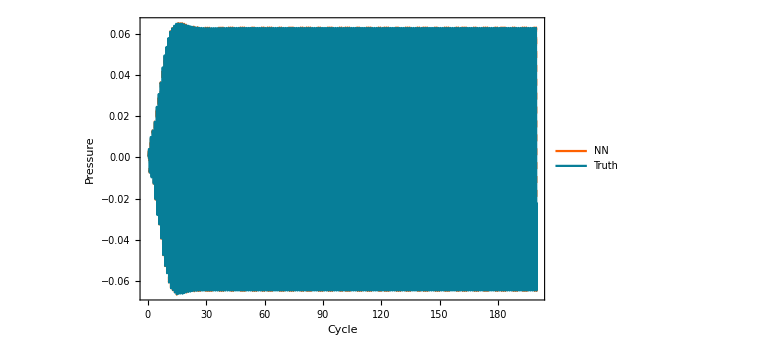
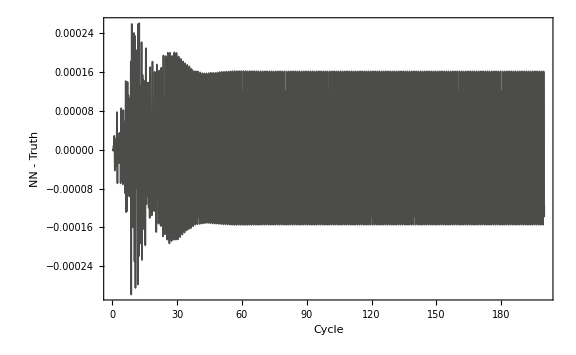
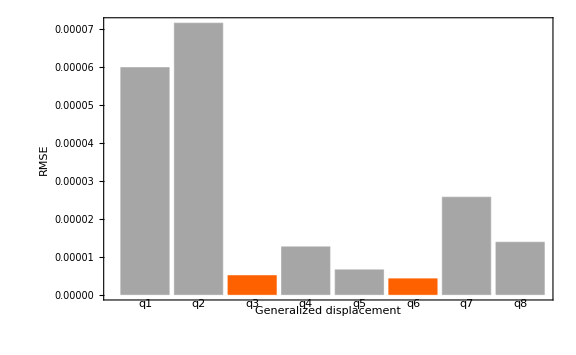
Full-modal Truth comparison from exported 200-cycle response
-Graphics-
-Graphics-
-Graphics-

```mathematica
Module[{baseDir,candidateDirs,pressureName,modalName,dirHasSources,compareDir,pressureSourceFile,modalSourceFile,pressureTable,modalTable,pressureHeader,modalHeader,pressureDataCompare,modalDataCompare,pressureCol,modalCol,tauCompare,periodCompare,cyclesCompare,pNNCompare,pTruthCompare,pErrorCompare,qErrorCompare,qLabelsCompare,qRMSECompare,pressureRMSECompare,pressureNRMSECompare,nnColor,truthColor,errColor,pressurePlotCompare,pressureErrorPlotCompare,modalRMSEPlotCompare,compareSummary},baseDir=Quiet[Check[NotebookDirectory[],Directory[]]];If[!StringQ[baseDir],baseDir=Directory[]];pressureName="nn_true_rollout_compare_pressure_source.csv";modalName="nn_true_rollout_compare_modal_source.csv";candidateDirs=DeleteDuplicates[Select[{FileNameJoin[{baseDir,"cavity_dimensionless_single_nonparam_cases"}],FileNameJoin[{Directory[],"cavity_dimensionless_single_nonparam_cases"}],FileNameJoin[{Directory[],"Code","cavity_dimensionless_single_nonparam_cases"}],FileNameJoin[{ParentDirectory[baseDir],"cavity_dimensionless_single_nonparam_cases"}]},StringQ]];dirHasSources[d_]:=FileExistsQ[FileNameJoin[{d,pressureName}]]&&FileExistsQ[FileNameJoin[{d,modalName}]];compareDir=FirstCase[candidateDirs,d_/;dirHasSources[d],Missing["NotFound"]];If[MissingQ[compareDir],Print["ERROR: full-modal comparison source files are missing. Run the integration/export section first."];Print/@candidateDirs;Abort[];];pressureSourceFile=FileNameJoin[{compareDir,pressureName}];modalSourceFile=FileNameJoin[{compareDir,modalName}];pressureTable=Import[pressureSourceFile,"CSV"];modalTable=Import[modalSourceFile,"CSV"];pressureHeader=ToString/@First[pressureTable];modalHeader=ToString/@First[modalTable];pressureDataCompare=N[Rest[pressureTable]];modalDataCompare=N[Rest[modalTable]];pressureCol[name_]:=FirstPosition[pressureHeader,name,Missing["NotFound"]]⟦1⟧;modalCol[name_]:=FirstPosition[modalHeader,name,Missing["NotFound"]]⟦1⟧;tauCompare=pressureDataCompare⟦All,pressureCol["tau"]⟧;periodCompare=Max[tauCompare]/200.;cyclesCompare=tauCompare/periodCompare;pNNCompare=pressureDataCompare⟦All,pressureCol["NN"]⟧;pTruthCompare=pressureDataCompare⟦All,pressureCol["Truth"]⟧;pErrorCompare=pressureDataCompare⟦All,pressureCol["Error"]⟧;qLabelsCompare=StringReplace[Cases[modalHeader,h_/;StringEndsQ[h,"_NN"]],"_NN"->""];qErrorCompare=Transpose[Table[modalDataCompare⟦All,modalCol[q<>"_Error"]⟧,{q,qLabelsCompare}]];qRMSECompare=√(Mean/@Transpose[qErrorCompare^2]);pressureRMSECompare=√Mean[pErrorCompare^2];pressureNRMSECompare=pressureRMSECompare/StandardDeviation[pTruthCompare];nnColor=RGBColor[0.996078431372549,0.3803921568627451,0.];truthColor=RGBColor[0.027450980392156862,0.49411764705882355,0.596078431372549];errColor=RGBColor[0.2980392156862745,0.2980392156862745,0.29411764705882354];compareSummary=Association["sourceDirectory"->compareDir,"cycles"->{Min[cyclesCompare],Max[cyclesCompare]},"truthUsesFullModes"->True,"pressureRMSE"->pressureRMSECompare,"pressureNRMSE"->pressureNRMSECompare,"modalRMSE"->AssociationThread[qLabelsCompare->qRMSECompare]];Print[compareSummary];pressurePlotCompare=ListLinePlot[{Transpose[{cyclesCompare,pNNCompare}],Transpose[{cyclesCompare,pTruthCompare}]},Frame->True,Axes->False,PlotStyle->{{nnColor,Dashed,AbsoluteThickness[1.6]},{truthColor,AbsoluteThickness[1.4]}},PlotLegends->Placed[LineLegend[{nnColor,truthColor},{"NN","Truth"}],{0.86,0.86}],FrameLabel->{"Cycle","Pressure"},ImageSize->Large,PlotRange->All];pressureErrorPlotCompare=ListLinePlot[Transpose[{cyclesCompare,pErrorCompare}],Frame->True,Axes->False,PlotStyle->{errColor,AbsoluteThickness[1.2]},FrameLabel->{"Cycle","NN - Truth"},ImageSize->Large,PlotRange->All];modalRMSEPlotCompare=BarChart[qRMSECompare,ChartLabels->Placed[qLabelsCompare,Below],ChartStyle->Table[If[MemberQ[{3,6},i],nnColor,GrayLevel[0.65]],{i,Length[qLabelsCompare]}],Frame->True,Axes->False,FrameLabel->{"Generalized displacement","RMSE"},ImageSize->Large];{{"Full-modal Truth comparison from exported 200-cycle response"}, {pressurePlotCompare}, {pressureErrorPlotCompare}, {modalRMSEPlotCompare}}]
```